Naloga 1

```mathematica
v0={10,3}
GG=9.81
H=10

v[t]:=v0+a*t

a={0,-GG}
x0={0,H}
X[t_]:=x0+v0*t+(a*t^2)/2
```

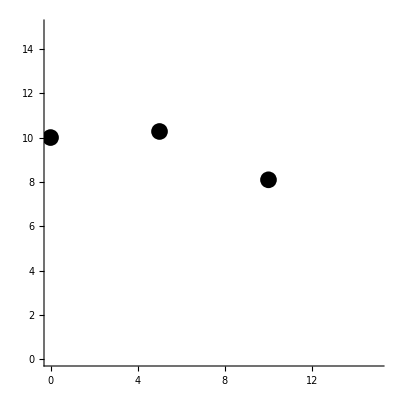

```mathematica
SlikaTocke[t_] := {PointSize[0.03],Point[X[t]]}
Graphics[{SlikaTocke[0],SlikaTocke[0.5],SlikaTocke[1]}, Axes->True, PlotRange->{{0,15},{0,15}}, AspectRatio->Automatic]
```

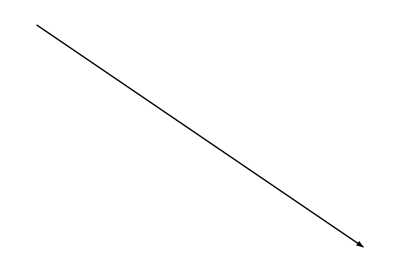

```mathematica
SlikaVektorja[t_] := {Arrow[{{0,0}, v[t]}]}
Table[Graphics[SlikaVektorja[1]], {i, {.05}}]
```

```mathematica
Manipulate[Graphics[SlikaTocke[t], Axes->True, PlotRange->{{0,20},{0,15}}, AspectRatio->Automatic],{t,0,3}]
```

```mathematica
časPadca =
```

```mathematica
časMaxVisine
```

```mathematica
maxVisina
```

```mathematica
absVrednost=
```

Naloga 2

```mathematica
Slika[Ravnina[n_, v_]] := Hyperplane[n, v]
Format[r_Ravnina] := Graphics3D[Slika[r]]


Normala[Ravnina[n_, v_]] := n

Tocka[Ravnina[n_, v_]] := v

r111 = Ravnina[{-1, -1, -1},{1, 1, 1}]
rx = Ravnina[{1, 0, 0}, {0, 0, 0}]
ry = Ravnina[{0, 1, 0}, {0, 0, 0}]
rz = Ravnina[{0, 0, 1}, {0, 0, 0}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
SlikaNormale[Ravnina[n_,v_]]:=Arrow[{v,v+n}]
```

```mathematica
Enacba[Ravnina[n_,v_]]:=
```

```mathematica
ResiSistem[sistem_List]:=
```

```mathematica
Presecisca[ravnine_List]:=
```

```mathematica
Vsebuje[Ravnina[n_,v_],x_,y_,z_,eps_:0.000001]:=
```

```mathematica
Trikotnik[r_Ravnina, tocke_List]:=
```

```mathematica
SlikaTrikotnikov[r1_,r2_,r3_,r4_]
```